### Exercise 1

#### The Black-Scholes function: Definitions

```mathematica
(*Normal CDF*)
Φ[x_]:=CDF[NormalDistribution[0,1],x]
```

```mathematica
(*Black-Scholes thresholds*)
dp[S_,τ_,K_,r_,δ_,σ_]:=1/(σ √τ)*(Log[S/K]+(r-δ+σ^2/2)*τ)
dm[S_,τ_,K_,r_,δ_,σ_]:=1/(σ √τ)*(Log[S/K]+(r-δ-σ^2/2)*τ)
```

```mathematica
(*Put option price*)
BSPut[S_,t_,K_,T_,r_,δ_,σ_]:=-S*Exp[-δ*(T-t)]*Φ[-dp[S,T-t,K,r,δ,σ]]+K*Exp[-r*(T-t)]*Φ[-dm[S,T-t,K,r,δ,σ]]
```

```mathematica
(*Put option delta*)
BSDeltaPut[S_,t_,K_,T_,r_,δ_,σ_]:=-Exp[-δ*(T-t)]*Φ[-dp[S,T-t,K,r,δ,σ]]
```

#### Parameter values

```mathematica
(*Parameter values*)
μ=0.052;
σ=0.12;
δ=0.00;
r=0.01;
```

```mathematica
(*Strike of the option*)
K=8000.0;
(*Initial portfolio price*)
X0=10000;
(*Maturity of the option*)
T=0.25;
```

```mathematica
(*Black-Scholes price of the put*)
p0=BSPut[X0,0,K,T,r,δ,σ]//N
```

0.0107703

```mathematica
(*Theoretical CDF of the random variable Subscript[V, 3M] assuming continuous rebalancing*)
CDFV[y_]:=If[y+Exp[r T]p0≥ 8000,Φ[-1/(σ T^(1/2))Log[(Exp[μ T]X0)/(y+Exp[r T]p0)]+σ/2 T^(1/2)],0]
```

#### Delta hedging at a daily frequency

```mathematica
(*Number of time points*)
Nt=90;
(*Time step*)
Δ=1/360.0;
(*Square root of time step*)
sqrΔ=Δ^(1/2);
(*Number of Simulations*)
Nb=100000;
```

```mathematica
(*Generate the matrix of BM increments*)
ΔZ=ParallelTable[RandomReal[NormalDistribution[],Nt],{k,1,Nb,1}];
```

```mathematica
(*Generate the matrix of stock paths*)
S=ConstantArray[0,{Nb,Nt+1}];
S[[All,1]]=X0;
For[k=2,k≤Nt+1,k++,S[[All,k]]=S[[All,k-1]]Exp[(μ-δ-σ^2/2)Δ+σ*sqrΔ*ΔZ[[All,k-1]]];]
```

```mathematica
(*Generate the matrix of portfolio value paths*)
V=ConstantArray[0,{Nb,Nt+1}];
V[[All,1]]=X0;
For[k=2,k≤Nt+1,k++,
V[[All,k]]=Exp[r*Δ]*V[[All,k-1]]+(1+BSDeltaPut[S[[All,k-1]],(k-2)*Δ,K,Nt*Δ,r,0,σ])(S[[All,k]]-Exp[r*Δ]S[[All,k-1]]);]
```

```mathematica
(*Extract the terminal portfolio value for each path*)
Data=V[[All,Nt+1]];
```

```mathematica
(*Clear memory*)
Clear[ΔZ,S,V]
```

```mathematica
(*Compare the PDFs*)
PD1=Show[
Histogram[Select[Data,#≤12000&],25,"PDF",AxesLabel->{"V_T","PDF"},ChartStyle->Lighter[Lighter[Lighter[Lighter[Blue]]]]],
Plot[{CDFV'[y]},{y,7000,12000},AxesOrigin->{Nb*K-p0 Exp[r*T],0},PlotStyle->{Darker[Blue],Thick},AxesLabel->{"Terminal value","PDF"}],PlotRange->All];
```

```mathematica
(*Compare the CDFs*)
PD2=Show[
Histogram[Select[Data,#≤12000&],25,"CDF",AxesLabel->{"V_T","CDF"},ChartStyle->Lighter[Lighter[Lighter[Lighter[Blue]]]]],
Plot[{CDFV[y]},{y,7000,12000},AxesOrigin->{Nb*K-p0 Exp[r*T],0},PlotStyle->{Darker[Blue],Thick},AxesLabel->{"Terminal value","PDF"}],PlotRange->All];
```

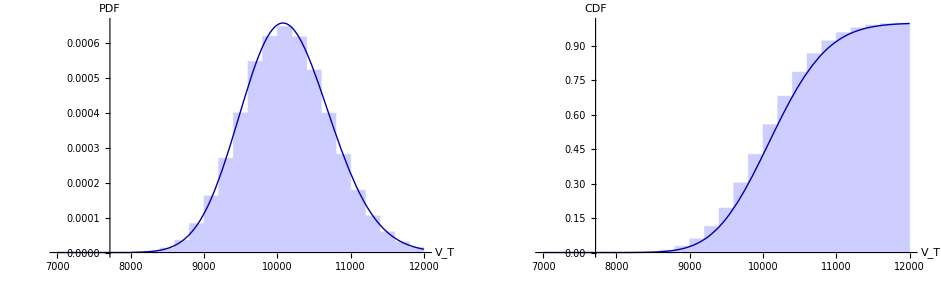

```mathematica
GraphicsGrid[{{PD1,PD2}}]
```

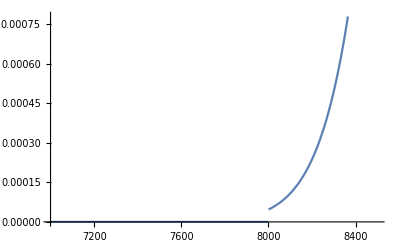

```mathematica
Plot[{CDFV[y]},{y,7000,8500}]
```